# CODE THREEDEE

## Input

```mathematica
{JA,JB,Nlj,δ,nstep, Nr,Nθ,Nϕ}={1,1.5,1,0.1,130,16,16,16};
{SF,n,l,j,nrel}={1,1,2,2.5,0};
{MA,ZA,Ma,Za,T,LmaxA,RcA}={23,9,1.00727,1,289,60,1.25};
{MB,ZB,Mc,Zc,Qfree,LmaxB,RcB}={MA-1,ZA-1,Ma,Za,0,40,1.25};
{Md,Zd,Rcutlow,LmaxC,RcC}={Ma,Ma,0,40,1.25};
{τ,Sp,V0,Vs}={1,13.26,0,12}; (* τ: -1 = neutron, 1 = proton, 2=d, 3=t, 4=3He, 5 4He*)
{Rrb,Rib,arb,aib,Rc}={1.27,1.27,0.67,0.67,1.25};
{Tc,θc,θd,βd}={100,50,-50,0};
(***************************************)
ep={T,Qfree,LmaxC,Sp};
mxnstep = nstep+4;
mxr = mxnstep δ;
spina=0.5;
spinb=0.5;
spinc=0.5;
spind=0.5;
h1=δ MB/MA; (* a+A *)
h2=δ;(* c+B *)
h3=δ;(* d+B *)
h4=δ;(* b+B *)
rmax1=mxr MB/MA;
rmax2=mxr;
rmax3=mxr;
rmax4=mxr;
```

```mathematica
mp=938.272;
amu=931.502014;931.5;
ℏc=197.328598;
```

## LGAUSS.f

```mathematica
LGAUSS[Nr_]:=Module[{root,xi,DP,wg},
root= Sort[Solve[LegendreP[Nr, x] == 0, {x}] // N];
xi=x/.root;
DP=Evaluate[D[LegendreP[Nr,x],x]]/.root;
wg=2/((1-xi^2)DP^2);
Table[{xi[[i]],wg[[i]]},{i,1,Nr}]
]
```

```mathematica
LGAUSS[16]//TableForm
```

-0.989401 | 0.0271525
-0.944575 | 0.0622535
-0.865631 | 0.0951585
-0.755404 | 0.124629
-0.617876 | 0.149596
-0.458017 | 0.169157
-0.281604 | 0.182603
-0.0950125 | 0.189451
0.0950125 | 0.189451
0.281604 | 0.182603
0.458017 | 0.169157
0.617876 | 0.149596
0.755404 | 0.124629
0.865631 | 0.0951585
0.944575 | 0.0622535
0.989401 | 0.0271525

## DLM.f (winger D-matrix)

```mathematica
DLM[l_,m_,cosθ_]:=√(((l-m)!)/((l+m)!))LegendreP[l,m,cosθ]
```

## Generate Guassian

```mathematica
tempr=LGAUSS[Nr];
wr=Table[(mxr-Rcutlow)/2 tempr[[i,2]],{i,1,Nr}]
radius=Table[(mxr+Rcutlow)/2+(mxr-Rcutlow)/2 tempr[[i,1]],{i,1,Nr}]
tempθ=LGAUSS[Nθ];
wθ=Table[tempθ[[i,2]],{i,1,Nθ}]
cθ=Table[tempθ[[i,1]],{i,1,Nθ}]
sθ=Table[√(1-cθ[[i]]^2),{i,1,Nθ}];
fac=√((2l+1)/(4π));
gθ=Table[fac DLM[l,mm,cθ[[i]]] wθ[[i]],{i,1,Nθ},{mm,0,l}];
TableForm[gθ,TableDepth->1]
tempϕ=LGAUSS[Nϕ];
wϕ=Table[π/2 tempϕ[[i,2]],{i,1,Nϕ}]
cϕ=Table[π/2+π/2 tempϕ[[i,1]],{i,1,Nϕ}]
sϕ=Table[√(1-cϕ[[i]]^2),{i,1,Nϕ}];
kr=Table[
temp=radius[[i]];
j=IntegerPart[temp/δ];
If[j< nstep-1,{j+1,temp/δ-j,1-temp/δ+j},{1,0,0} ]
,{i,1,Nr}]
```

{0.181921,0.417099,0.637562,0.835014,1.00229,1.13335,1.22344,1.26932,1.26932,1.22344,1.13335,1.00229,0.835014,0.637562,0.417099,0.181921}

{0.0710137,0.371347,0.900271,1.63879,2.56023,3.63129,4.81326,6.06342,7.33658,8.58674,9.76871,10.8398,11.7612,12.4997,13.0287,13.329}

{0.0271525,0.0622535,0.0951585,0.124629,0.149596,0.169157,0.182603,0.189451,0.189451,0.182603,0.169157,0.149596,0.124629,0.0951585,0.0622535,0.0271525}

{-0.989401,-0.944575,-0.865631,-0.755404,-0.617876,-0.458017,-0.281604,-0.0950125,0.0950125,0.281604,0.458017,0.617876,0.755404,0.865631,0.944575,0.989401}

{0.0165856,0.00301371,0.000221154}
{0.0329201,0.0149139,0.00259173}
{0.0374538,0.0318617,0.00921441}
{0.0279829,0.0476581,0.02067}
{0.00685607,0.0561464,0.0357244}
{-0.019775,0.0532072,0.0516336}
{-0.0438904,0.0381181,0.0649415}
{-0.0581329,0.0138431,0.0725193}
{-0.0581329,-0.0138431,0.0725193}
{-0.0438904,-0.0381181,0.0649415}
{-0.019775,-0.0532072,0.0516336}
{0.00685607,-0.0561464,0.0357244}
{0.0279829,-0.0476581,0.02067}
{0.0374538,-0.0318617,0.00921441}
{0.0329201,-0.0149139,0.00259173}
{0.0165856,-0.00301371,0.000221154}

{0.042651,0.0977876,0.149475,0.195767,0.234985,0.26571,0.286833,0.297588,0.297588,0.286833,0.26571,0.234985,0.195767,0.149475,0.0977876,0.042651}

{0.016649,0.0870614,0.211066,0.38421,0.600239,0.851345,1.12845,1.42155,1.72004,2.01314,2.29025,2.54135,2.75738,2.93053,3.05453,3.12494}

{{1,0.710137,0.289863},{4,0.713473,0.286527},{10,0.00270944,0.997291},{17,0.387905,0.612095},{26,0.602292,0.397708},{37,0.312876,0.687124},{49,0.132562,0.867438},{61,0.634162,0.365838},{74,0.365838,0.634162},{86,0.867438,0.132562},{98,0.687124,0.312876},{109,0.397708,0.602292},{118,0.612095,0.387905},{125,0.997291,0.00270944},{1,0,0},{1,0,0}}

## RK4

```mathematica
WS[r_,V_,R_,a_]:=V/(1+Exp[(r-R)/a])
OpticalPotential[vBE_,vWS_,rWS_,aWS_,vLS_,rLS_,aLS_,vCoul_,r_]:=vBE-vWS/(1+Exp[(r-rWS)/aWS])-vLS/r Exp[(r-rLS)/aLS]/(1+Exp[(r-rLS)/aLS])^2+vCoul/r
RK4SE[U_Symbol,m_,T_,l_,v0_,rRange_,nStep_]:=Module[
{G,k,kv,kx,h,SolU,SolR,dx,dv,g1,g2,norFac,MaxU,MaxJ,MaxR},
k=√((2 m T)/ℏc^2);
G[r_,u_,v_]:=(2m)/ℏc^2(U[r]-T)u+(l(l+1))/r^2 u;
kv={0,0,0,0};
kx={0,0,0,0};
h=(rRange[[2]]-rRange[[1]])/nStep;
SolU=Table[{ρ,0,0},{ρ,rRange[[1]],rRange[[2]],h}];
SolU[[1,2]]=0; (* u[0] = 0  for convergence *)
SolU[[1,3]]=v0;
Print[{"k",k,"λ",(2π)/k,"step",h,"nStep+1",nStep+1}];
Monitor[Table[
kv[[1]]=G[SolU[[i,1]],SolU[[i,2]],SolU[[i,3]]];
kx[[1]]=SolU[[i,3]];
kv[[2]]=G[SolU[[i,1]]+h/2,SolU[[i,2]]+kx[[1]] h/2, SolU[[i,3]]+kv[[1]] h/2];
kx[[2]]=SolU[[i,3]]+kv[[1]] h/2;
kv[[3]]=G[SolU[[i,1]]+h/2,SolU[[i,2]]+kx[[2]] h/2, SolU[[i,3]]+kv[[2]] h/2];
kx[[3]]=SolU[[i,3]]+kv[[2]] h/2;
kv[[4]]=G[SolU[[i,1]]+h,SolU[[i,2]]+kx[[3]] h, SolU[[i,3]]+kv[[3]] h];
kx[[4]]=SolU[[i,3]]+kv[[3]]h;
dx=h/6(kx[[1]]+2kx[[2]]+2kx[[3]]+kx[[4]]);
dv=h/6(kv[[1]]+2kv[[2]]+2kv[[3]]+kv[[4]]);
SolU[[i+1,3]]=SolU[[i,3]]+dv;
SolU[[i+1,2]]=SolU[[i,2]]+dx;
(*Print[{k,dx,SolU[[i]]}];*)
,{i,1,nStep}],i];
MaxU=Max[SolU[[1;;-1,2]]];
MaxJ=MaxValue[k r SphericalBesselJ[l,k r],{r}];
norFac=MaxJ/MaxU;
Print[{"Max u_l",MaxU,"Max ρJ",MaxJ,"norm",norFac}];
SolU=Table[{SolU[[i,1]],norFac SolU[[i,2]],norFac SolU[[i,3]]},{i,1,nStep+1}];
SolR=Table[{SolU[[i,1]],SolU[[i,2]]/SolU[[i,1]],SolU[[i,3]]/SolU[[i,1]]-SolU[[i,2]]/SolU[[i,1]]^2},{i,nStep+1}];
MaxR=Max[SolR[[1;;-1,2]]];
g1=ListPlot[
Table[SolR[[i,1;;2]],{i,1,Length[SolU]}]
,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["r [fm]",18],Style["R_l",18]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotRange->1.1{-MaxR,MaxR}];
g2=Plot[{0.01(U[r]+ℏc^2/(2m)(l(l+1))/r^2),0.01T},{r,rRange[[1]],rRange[[2]]},PlotStyle->{Red,Green},PlotRange->All];
Print[Show[{g1,g2},ImageSize->600]];
{SolR,SolU}
]
```

{k,0.694208,λ,9.05087,step,0.09995,nStep+1,201}

{Max u_l,1741.43,Max ρJ,1.11082,norm,0.000637878}

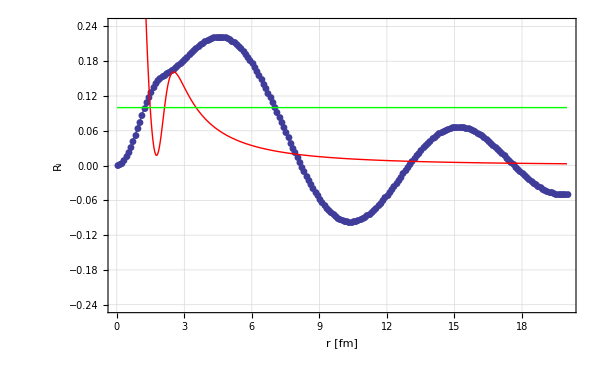

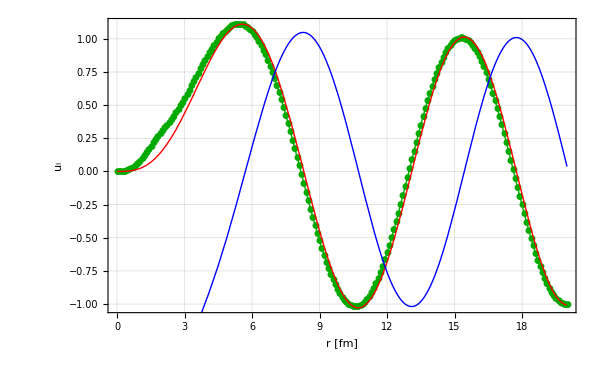

```mathematica
Upot[r_]:=WS[r,-50,2,0.2]
AngularL=2;
tRange={0.01,20};
Energy=10;
test=RK4SE[Upot,mp,Energy,AngularL,0.5,tRange,200];
k=√((2 mp Energy)/ℏc^2);
Show[
ListPlot[test[[2,1;;-1,{1,2}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["r [fm]",18],Style["u_l",18]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotStyle->Darker[Green]],
Plot[{k r SphericalBesselJ[AngularL,k r],
k r SphericalBesselY[AngularL,k r]},{r,0,tRange[[2]]},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]}]
]
```

## BDSTS.f (bounded state)

```mathematica
Func[x_]:=2(IntegerPart[x/2+0.1])-x+1/2
Potential[vBE_,vWS_,rWS_,aWS_,vLS_,rLS_,aLS_,vCoul_,vLsq_,r_]:=vBE-vWS/(1+Exp[(r-rWS)/aWS])-vLS/r Exp[(r-rLS)/aLS]/(1+Exp[(r-rLS)/aLS])^2+vCoul/r+vLsq/r^2
F1BDST[Rc_,x_,a5_,a6_]:=Piecewise[{{1/x,x≥ Rc},{a5+a6 x^2,x<Rc}}] (* Coulomb Potential *)

BDSTS[eb1i_,eb2i_,Vni_,Vsoi_, Rn_,An_,Rs_,As_,Rcoul_,Rmn_,Zn_,n_,l_,Ru_,h_,tol_,mode_]:=Module[
{eb1,eb2,Vn,Vso,Rmb,Zb,anL,ne,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a910,a78,Rne,Rse,Rcoule,Rmu,eba,damp,vbs1,vbs2,vbs3,vbs4,vbs5,Rext,NRext,Rmax,NRmax,NRu,Rx,RecRx,Fr,Gr,PT,Rroot,Rcutoff,Rmtch,NRmtch,n1,n2,n3,n4,n5,b1,b2,b3,b4,b5,b6,Ybs,IP,Hsq,hd3,Icycle,Iter,Iubd1,Y,YD,F,Nod,SRul,SRulD,NRup1,NRx,src,RK1,s2,s3,Jcycle,IS,he,Inc,
nul,nulm3,kl,isrc,index1,index2 ,ENL,Rlmda,Loop78,Loop79},
{eb1,eb2,Vn,Vso}={eb1i,eb2i,Vni,Vsoi};
Rmb=1.0076;Zb=1;
anL=0;
ne=n-1;
a1=(Rmn-Rmb)^(1/3);
Rne=Rn a1;(* radius of Ucent B *)
Rse=Rs a1;(* radius of Uls B *)
Rcoule=Rcoul a1;
Rmu=(Rmn-Rmb) Rmb/Rmn;
(*Print["{anL,ne}"<>ToString[{anL,ne}]];
Print["{Rne,Rse,Rcoule,Rmu}"<>ToString[{Rne,Rse,Rcoule,Rmu}]];*)
a2=0.0478326 Rmu;
a3=2 a2 Vso/As;
If[mode==3,eb2=0];
If[mode==4,eb1=0];
a4=Max[1.5(Zn-Zb)Zb/Rcoule+200((ne+0.5(l+1))^2/(Rmu Rne^2)),5];
(*Print["{a1,a2,a3,a4}"<>ToString[{a1,a2,a3,a4}]];*)
If[Vn<0.0001,Vn=eb1+eb2+a4];
eba=eb1+eb2;
damp=Min[0.9,Max[0.1(Vn-eba)/eba,1.1 tol]];
(*Print["{eba,damp}"<>ToString[{eba,damp}]];*)
vbs1={a2 eb1,a2 eb2};
vbs2=a2 Vn;
vbs3={a3 l,-a3 l-a3};
vbs4=0.0688724 Rmu Zb (Zn-Zb);
vbs5=l(l+1);
(*Print["{vbs1,vbs2,vbs3,vbs4,vbs5}"<>ToString[{vbs1,vbs2,vbs3,vbs4,vbs5}]];*)

Rext=11.53 An +Rne;(*Print["Rext' = "<>ToString[Rext]];*)
NRext=IntegerPart[Rext/h+0.5];
If[Func[NRext]≤0, NRext = NRext+1];
Rext=NRext h;
Print["Rext = "<>ToString[Rext]];

Rmax=Max[Ru,2 Rext];(*Print["Rmax' = "<>ToString[Rmax]];*)
NRmax=IntegerPart[Rmax/h+0.5];
If[Func[NRmax]≤0,NRmax=NRmax+1];
Rmax=NRmax h;
Print["Rmax = "<>ToString[Rmax]];

NRu=IntegerPart[Ru/h+0.5];
If[Func[NRu]≤0,NRu=NRu+1];
(*Print["NRu = "<>ToString[NRu]];*)

a5=1.5/Rcoule;
a6=-0.5/Rcoule^3;
a7={Exp[h/An],Exp[h/As]};
a8={1/a7[[1]],1/a7[[2]]};
a9={Exp[-Rne/An],Exp[-Rse/As]};
a10={Exp[(Rext-Rne)/An],Exp[(Rext-Rse)/As]};
(*Print["{a5,a6,a7,a8,a9,a10}"<>ToString[{a5,a6,a7,a8,a9,a10}]];*)

Rx=Rext;
a910={a10[[1]],a10[[2]]};
(*Print["{Rctoff,Rx,a910}"<>ToString[{Max[Rne,Rcoule],Rx,a910}]];*)

Rmtch=Max[
Rroot=x/.FindRoot[Potential[vbs1[[1]]+vbs1[[2]],vbs2,Rne,An,Total[vbs3],Rse,As,vbs4,vbs5,x]==0,{x,Rne}],
Rcutoff=Max[Rne,Rcoule]
];(*
Label[findRmtch];Rx=Rx-h;
If[Rx> Max[Rne,Rcoule],
RecRx=1/Rx;
a910={a910[[1]]a8[[1]],a910[[2]]a8[[2]]};
Fr=1/(1+a910[[1]]);
Gr=RecRx a910[[2]]/(1+a910[[2]])^2;
PT=vbs1[[1]]+vbs1[[2]]-vbs2 Fr-Total[vbs3]Gr+vbs4 RecRx+vbs5 RecRx^2;
(*Print["{Rx,PT}"<>ToString[{Rx,PT}]];*)
If[PT≤ 0,Rmtch=Rx, Goto[findRmtch]];,
Rmtch=Rx;
];*)
NRmtch=IntegerPart[Rmtch/h+0.5];
If[Func[NRmtch]≤0,NRmtch=NRmtch+1];
Rmtch=NRmtch h;
Print["{Rroot,Rcutoff, Rmtch} = "<>ToString[{Rroot,Rcutoff,Rmtch}]];


n1=NRmtch;
n2=NRext-NRmtch;
n3=NRmax-NRext;
If[mode==3,n4=1;n5=1;];
If[mode==4,n4=2;n5=2;];
(*Print["{n1,n2,n3,n4,n5}"<>ToString[{n1,n2,n3,n4,n5}]];*)

b5={{0,0},{0,0}};
IP=NRu+1;
Ybs={Table[0,{i,1,IP}],Table[0,{i,1,IP}]};

Do[
Ybs[[i,2]]=(-1)^ne h^(l+1);
,{i,n4,n5}];

Hsq=h^2;
hd3=h/3;
Icycle=0;
Iter=-1;
Iubd1=0;

(*vbs1={a2 eb1,a2 eb2};*)
b1={0,0};
b2={0,0};
b3={{0,0},{0,0}};
b4={0,0};
b5={{0,0},{0,0}};
b6={{0,0},{0,0}};
F=Table[0,{i,1,2},{j,1,7}];
Nod={0,0};
Y={{0,0},{0,0}};
YD={{0,0},{0,0}};
SRul={{{0,0},{0,0}},{{0,0},{0,0}}};
SRulD=Table[0,{i,1,8}];
Rlmda={0,0};

Rx=Rmax;
Table[
b1[[i]]=√vbs1[[i]];
b2[[i]]=0.5 vbs4/b1[[i]];
s2=1;
s3=1;
F[[i,3]]=s3 Exp[-b1[[i]] Rx-b2[[i]] Log[2 b1[[i]] Rx]];
F[[i,2]]=s2 Exp[-b1[[i]](Rx-h)-b2[[i]]Log[2 b1[[i]](Rx-h)]];
b4[[i]]=0;
If[NRmax≤ NRu,
Ybs[[i,NRmax+1]]=F[[i,3]];
Ybs[[i,NRmax]]=F[[i,2]];
];
,{i,n4,n5}];
(*Print[{"Ybs",Ybs}];
Print[{"F",F}];*)

(*Print["{NRext, NRmax = NRx, NRu, NRmtch}"<>ToString[{NRext, NRmax,NRu, NRmtch}]];*)
NRup1=NRu+1;
NRx=NRmax;
src=4.0;
(*Print[{"Rx",Rx}];*)
Table[
Rx=Rmax-i h;
(*RecRx=1/Rx;*)
NRx=NRmax-i;
RK1=vbs4/Rx+vbs5/Rx^2;
Table[
b1[[j]]=RK1+vbs1[[j]];
F[[j,1]]=(2+h^2 b1[[j]])F[[j,2]]-F[[j,3]];
If[NRx≤ NRup1,Ybs[[j,NRx]]=F[[j,1]]];
b4[[j]]=b4[[j]]+src (F[[j,2]])^2;
F[[j,3]]=F[[j,2]];
F[[j,2]]=F[[j,1]];
,{j,n4,n5}];
(*Print[{i,"src, Rx, NRx", src, Rx, NRx}];*)
src=6-src;
,{i,1,n3}];
(*Print[{"b1, b4",b1,b4}];
Print[{"Ybs",Ybs}];
Print[{"F",F}];*)



Do[
b6[[i,2]]=F[[i,3]];
b6[[i,1]]=F[[i,2]];
b4[[i]]=h/3(b4[[i]]-F[[i,3]]^2);
,{i,n4,n5}];
(*Print[{"b6, b4", b6, b4}];*)

Label[Loop78];(*Print["Loop78"];*)
Jcycle=0;
Label[Loop79];(*Print["Loop79"];*)
(*Print[{"vbs2",vbs2,"a3",a3,"vbs3",vbs3}];*)
vbs2=a2 Vn;
a3=2 a2 Vso/As;
vbs3={a3 l, -a3 l -a3};

Table[
IS;
src=4.0;
If[IS≤ 1.5,
a78=a7;
a910=a9;
Rx=0;
he=h;
NRx=2;
Inc=1;
nul=n1+2;
nulm3=nul-3;
kl=5;
isrc=1;
index1=0;
index2=2;
Table[
F[[i,6]]=Ybs[[i,1]];
F[[i,7]]=Ybs[[i,2]];
SRulD[[index1+i]]=0;
,{i,n4,n5}];
];
If[IS> 1.5,
a78=a8;
a910=a10;
Rx=Rext;
he=-h;
NRx=NRext;
Inc=-1;
nul=n2+2;
nulm3=nul-3;
kl=5;
isrc=1;
index1=4;
index2=6;
Table[
F[[i,6]]=b6[[i,2]];
F[[i,7]]=b6[[i,1]];
SRulD[[index1+i]]=0;
SRulD[[index2+i]]=0;
,{i,n4,n5}];
];

(*Print[{"====================IS", IS, "Rx", Rx, "nul", nul}];*)
(*Print[{"F",F}];*)
(*Print[{"he",he,"inc",Inc, "a78",a78,"a910",a910}];*)

Do[
Rx=Rx+he;
NRx=NRx+Inc;
a910={a910[[1]]a78[[1]],a910[[2]]a78[[2]]};
Fr=1/(1+a910[[1]]);
Gr=1/Rx a910[[2]]/(1+a910[[2]])^2;
RK1=-vbs2 Fr + vbs5/Rx^2;
(*Print[{"RK1 b4:", RK1,"vbs2", vbs2,"vbs5",vbs5,"Rx",Rx, "F1BDST",F1BDST[Rcoule,Rx,a5,a6]}];*)
If[IS≤ 1.5,
RK1=RK1+vbs4 F1BDST[Rcoule,Rx,a5,a6];,
RK1=RK1+vbs4/Rx;
];
If[nulm3≤ i,
kl=kl-1;
isrc=isrc-1;
];

(*Print[{"a910",a910,"Fr",Fr,"Gr",Gr,"RK1",RK1}];*)

Do[
(*Print[{"=========i",i,,"nulm3",nulm3,"kl,",kl, "F b4", F}];*)
Do[F[[j,k]]=F[[j,k+1]],{k,kl,6}];
(*Print[{"F af", F}];*)
b1[[j]]=RK1+vbs1[[j]]-vbs3[[j]] Gr;
F[[j,7]]=(2+h^2 b1[[j]])F[[j,6]]-F[[j,5]];
(*Print[{"F end", F}];*)
If[IS<1.5 && F[[j,6]]F[[j,5]]<0, Nod[[j]]=Nod[[j+1]]];
b2[[j]]=src (   F[[j,6]]  )^2;
If[Iter≥0, 
ENL=1;
If[NRx≤ NRu+1, Ybs[[j,NRx]]=F[[j,7]] ENL];
b5[[j,IS]]=b5[[j,IS]]+b2[[j]] ENL^2;
];
SRulD[[index1+j]]=SRulD[[index1+j]] + vbs2 Fr b2[[j]];
,{j,n4,n5}];
(*Print[{"b1", b1, "b2", b2, "b5",b5, "SRulD", SRulD}];*)

If[isrc<0, src=0];
If[isrc==0, src=1];
If[isrc>0, src=6-src];
,{i,1,nul}];
Do[
Y[[i,IS]]=F[[i,4]];
YD[[i,IS]]=(1/60(F[[i,7]]-F[[i,1]])+0.15(F[[i,2]]-F[[i,6]])+0.75(F[[i,5]]-F[[i,3]]))/he;
If[Iter>0,b5[[i,IS]]=h/3 b5[[i,IS]]];
SRul[[i,1,IS]]=h/3 SRulD[[index1+i]];
,{i,n4,n5}];
(*Print[{"F", F}];*)
,{IS,1,2}];
(*Print[{"******************************** iter", Iter}];
Print[{"Y",Y}];
Print[{"YD",YD}];
Print[{"Rlmda",Rlmda}];*)
If[Iter≤0,
Do[
If[ne<Nod[[i]] || ne > Nod[[i]], 
Jcycle=Jcycle+1;
If[Jcycle≤5,
Vn=Abs[Vn+5Sign[ne-Nod[[n4]]]];
Print["Goto:Loop79"];
Goto[Loop79];,
Print["STOP ne = Nod"];
Return[];
],
Break[];
];
,{i,n4,n5}];
Do[
b1[[i]]=(Y[[i,2]]/Y[[i,1]])^2;
b2[[i]]=Y[[i,2]]YD[[i,2]]-Y[[i,1]]YD[[i,1]]b1[[i]];
,{i,n4,n5}];

Icycle=Icycle+1;

If[Icycle>20,
FFF=Max[Abs[Rlmda]];
Iter = Iter+2;
Print["STOP Icylce>20"];Return[];
];
If[Icycle≤20,
Rlmda={b2[[n4]]/(b1[[n4]]SRul[[n4,1,1]]+SRul[[n4,1,2]]),0};
If[Max[Abs[Rlmda]]≥1,
Iubd1=Iubd1+1;
If[Iubd1>5, Print["STOP Iubd1>5"];Return[];]
];
If[Abs[Rlmda[[1]]]>damp,Rlmda[[1]]=damp Sign[Rlmda[[1]]];];
If[Abs[Rlmda[[2]]]>damp,Rlmda[[2]]=damp Sign[Rlmda[[2]]];];
Vn=(1-Rlmda[[1]])Vn;
Vso=(1-Rlmda[[2]])Vso;
Print[{"Icycle",Icycle,"Vn,Vso,eb1,eb2",Vn,Vso,eb1,eb2}];
(*Print[{"Rlmda",Rlmda}];*)
If[Abs[Rlmda[[1]]]≤ tol && Abs[Rlmda[[2]]]≤ tol, Iter=Iter+2;];
(*Print["Goto:Loop78"];*)
Goto[Loop78];
];
]
If[Iter>0,
nul=Min[n1-3,NRup1];
Print[{"Final Val", "Vn,Vso,eb1,eb2",Vn,Vso,eb1,eb2}];
Do[
b1[[i]]=Y[[i,2]]/Y[[i,1]];
b5[[i,1]]=b1[[i]] b1[[i]] b5[[i,1]];
b2[[i]]=√(1/(b5[[i,1]]+b5[[i,2]]+b4[[i]]));
b4[[i]]=b1[[i]] b2[[i]];
(*Print[{"b1,b2,b5,b4", b1,b2,b5,b4}];*)
Do[
Ybs[[i,j]]=b4[[i]] Ybs[[i,j]];
,{j,1,nul}];
IP=nul+1;
Do[
Ybs[[i,j]]=b2[[i]]Ybs[[i,j]];
,{j,IP,NRup1}];
,{i,n4,n5}];
];
Print[
Plot[Potential[vbs1[[1]]+vbs1[[2]],vbs2,Rne,An,Total[vbs3],Rse,As,vbs4,vbs5,x],{x,1,Rmax},PlotRange->All]
];
{Table[{(i-1) h,Ybs[[n4,i]]},{i,1,NRu}], {Vn,Vso,eb1,eb2},{vbs1[[1]]+vbs1[[2]],vbs2,Rne,An,Total[vbs3],Rse,As,vbs4,vbs5}}
]
```

## Continuous...

Rext = 11.4

Rmax = 22.8

{Rroot,Rcutoff, Rmtch} = {3.35072, 3.55818, 3.6}

{Icycle,1,Vn,Vso,eb1,eb2,62.3856,12,13.26,0}

{Icycle,2,Vn,Vso,eb1,eb2,60.9051,12,13.26,0}

{Icycle,3,Vn,Vso,eb1,eb2,60.8172,12,13.26,0}

{Icycle,4,Vn,Vso,eb1,eb2,60.817,12,13.26,0}

{Final Val,Vn,Vso,eb1,eb2,60.817,12,13.26,0}

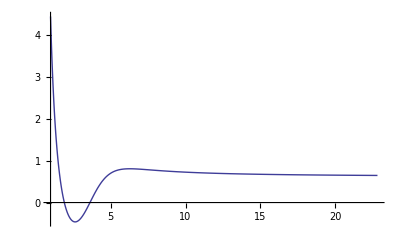

{60.817,12,13.26,0}

{0.611083,2.80274,3.55818,0.67,-1.6508,3.55818,0.67,0.530846,6}

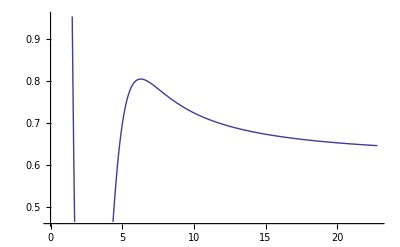

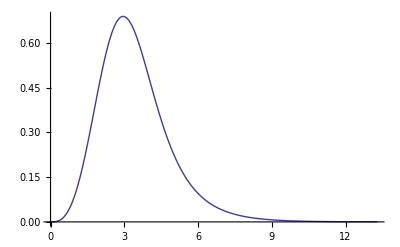

{RMS of Bound state,3.26203}

{0.00271457,0.016828,0.0544657,0.0982938,0.0990899,0.0505806,0.0141071,0.00311941,0.000691276,0.000164191,0.0000428677,0.0000124838,4.09092×10^-6,1.49633×10^-6,0.,0.}

```mathematica
If[j>l,mode=3];
If[j<l,mode=4];
k=mode-2;
eb={0,0};
eb[[k]]=ep[[4]];
BStateOuput=BDSTS[eb[[1]],eb[[2]],V0,Vs, Rrb,arb,Rib,aib,Rc,MA,ZA,n,l,rmax4,h4,0.001,mode];
BState=BStateOuput[[1]];
BStateOuput[[2]]
OptPar=BStateOuput[[3]]
Plot[OpticalPotential[OptPar[[1]],OptPar[[2]],OptPar[[3]],OptPar[[4]],OptPar[[5]],OptPar[[6]],OptPar[[7]],OptPar[[8]],r]+OptPar[[9]]/r^2,{r,0,22.8},PlotR]
ListPlot[BState,Joined->True,PlotRange->All]
{"RMS of Bound state",rms=√Sum[(BState[[i,1]]BState[[i,2]])^2 h4,{i,1,Length[BState]}]}
gr=Table[0,{i,1,nstep+1}];
Table[gr[[i]]=BState[[i,2]] SF,{i,1,nstep}];
bsr=Table[0,{i,1,Nr}];
Table[
il=kr[[i,1]];
bsr[[i]]=(kr[[i,2]] gr[[il+1]]+kr[[i,3]]gr[[il]]) wr[[i]]/(radius[[i]])^2;
,{i,1,Nr}];
bsr
```

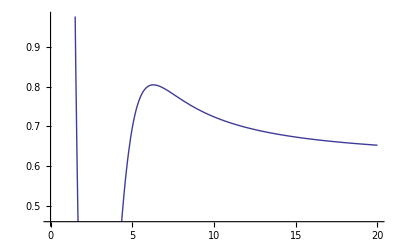

```mathematica
Plot[GG[r]+(l(l+1))/r^2,{r,0,20}]
```

{k,0.809578,λ,7.76106,step,0.06695,nStep+1,201}

{Max u_l,7039.03,Max ρJ,1.11082,norm,0.000157808}

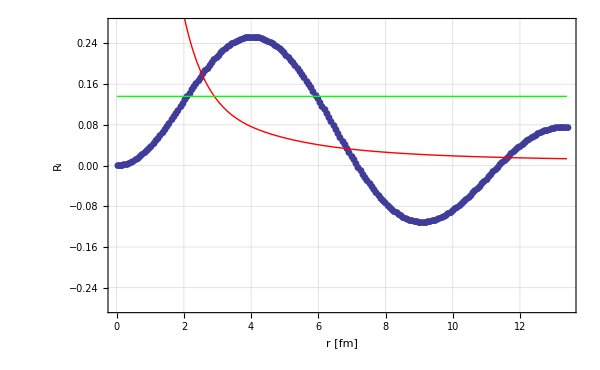

```mathematica
(*Upot[r_]:=WS[r,-50,2,0.2]*)
GG[r]:=OpticalPotential[OptPar[[1]],OptPar[[2]],OptPar[[3]],OptPar[[4]],OptPar[[5]],OptPar[[6]],OptPar[[7]],OptPar[[8]],r];
tRange={0.01,13.4};
Energy=13.6;
test=RK4SE[GG,mp,Energy,l,0.5,tRange,200];
k=√((2 mp Energy)/ℏc^2);
```

change dir.

/home/goluckyryan/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata

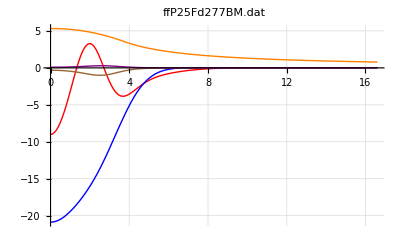

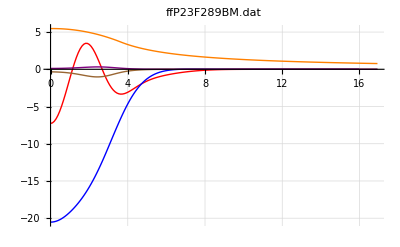

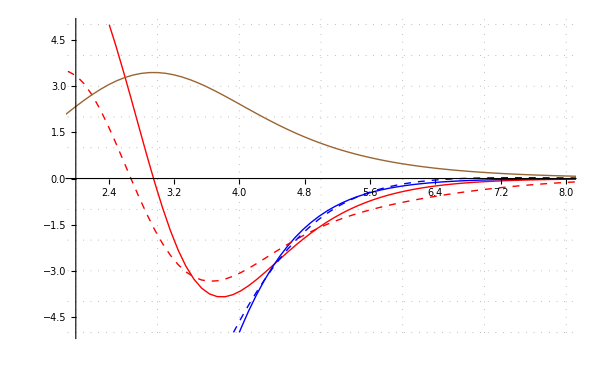

```mathematica
Dirac=EDAD2[MA,ZA,T,RcA,nstep+4,h1];
Ogata=GetOgata["ffP25Fd277BM.dat","DULS_25F277.dat",10,1];
Ogata=GetOgata["ffP23F289BM.dat","DULS_23F289.dat",10,1];
ListPlot[{
RePot[Dirac[[1]]],
ImPot[Dirac[[1]]],
RePot[Ogata[[1]]],
ImPot[Ogata[[1]]],
(*RePot[Ogata[[2]]],
ImPot[Ogata[[2]]],*)
Table[{BState[[i,1]],BState[[i,2]]5},{i,1,Length[BState]}]
},Joined->True,PlotRange->{{2,8},{-5,5}},ImageSize->600,
PlotStyle->{Red,Blue,Directive[Red,Dashed],Directive[Blue,Dashed],Brown},
GridLines->{Table[i,{i,2,8}],Table[i,{i,-5,5}]},GridLinesStyle->Directive[Gray,Dotted]]
```

## DSTWAV.f

```mathematica
DSTWAV[RmT_,ZT_,Rmp_,Zp_,Rc_,Ep_,h_,Rmax_,Lmax_,Iacd_,potID_]:=Module[
{Ydwc,SMatrix,pot,Ucent,Uls,Ucoul,LSFac,Dmp,DmT,Esum,DEp,DET,RMu,Epcm,NRmax,Rmtch,Imtch,NRmax1,jmaxp1,lmaxp1,a1,RKC,rkct1,rkct2,rkct3,ip1,ic,eta,zprod,RK1,RMu1,CoulFGS,Ucl,HLp,HLpD,HLm,HLmD,temp},
Dmp=Rmp amu;
DmT=RmT amu;
DEp=EcmP[RmT,Ep];
DET=EcmA[RmT,Ep];
Esum=DEp+DET;
RMu=(DEp DET)/(Esum amu);
Epcm=(DEp^2-Dmp^2)/(2 RMu amu);
(*Print[{Dmp,DmT,"Esum",Esum,"DEp",DEp,"DET",DET,"RMu",RMu,"Epcm",Epcm}];*)
NRmax=Floor[ Rmax/h+0.5];
NRmax1=NRmax+1;

a1=(2 amu RMu)/ℏc^2;
jmaxp1=2; (* spin 1/2 *)
lmaxp1=Lmax+1;
Print[{"NRmax",NRmax,"jmaxp1",jmaxp1,"lmaxp1",lmaxp1}];

Ydwc=Table[0,{j,1,jmaxp1},{i,1,NRmax1+1},{lp1,1,lmaxp1}];
Table[Ydwc[[j,1,2]]=1+ⅈ,{j,1,jmaxp1}];
Table[Ydwc[[j,2,lp1]]=10^-15+ⅈ 10^-15,{j,1,jmaxp1},{lp1,1,lmaxp1}];

pot=PotSet[RmT,ZT,Ep,Rc,NRmax1,h,potID];
Ucent=pot[[1]];
Uls=pot[[2]];
Ucoul=pot[[3]];
(*Print[{Length[Ucent],Length[Uls],Length[Ucoul]}];
Print[Ucent//TableForm];
Print[Uls//TableForm];
Print[Ucoul//TableForm];*)

rkct1=Table[0,{i,1,jmaxp1},{lp1,lmaxp1}];
rkct2=Table[0,{i,1,jmaxp1},{lp1,lmaxp1}];
rkct3=Table[0,{i,1,jmaxp1},{lp1,lmaxp1}];


LSFac[j_,l_]:=If[j==1,l,-(l+1)];

RKC[i_,j_,l_]:=If[i==1,
0,
1+h^2/12(a1(Epcm-Ucent[[i,2]]-Ucoul[[i,2]]-LSFac[j,l]Uls[[i,2]])-(l(l+1))/((i-1) h)^2)
];

Do[
Do[
rkct1[[j,lp1]]=0;
rkct2[[j,lp1]]=RKC[2,j,lp1-1];
,{j,1,jmaxp1}];,
{lp1,1,lmaxp1}];


Do[
Ydwc[[j,1,2]]==1+1 ⅈ;
rkct1[[j,2]]=-10^-15/6;
,{j,1,jmaxp1}];
(*Print[{a1 Epcm}];
Print[Table[{L,rkct1[[1,L]],rkct2[[2,L]]},{L,1,10}]];*)


Table[
rkct3[[j,lp1]]=RKC[i+1,j,lp1-1];
(*If[j==1&& lp1==2 && i<20,Print[{i,j,lp1,LSFac[j,lp1],Ucent[[i+1,2]],i h,(lp1-1)(lp1)/Ucent[[i+1,1]]^2,rkct3[[j,lp1]],rkct2[[j,lp1]],rkct1[[j,lp1]]}]];
*)
Ydwc[[j,i+1,lp1]]=((12-10 rkct2[[j,lp1]])Ydwc[[j,i,lp1]]-rkct1[[j,lp1]]Ydwc[[j,i-1,lp1]])/rkct3[[j,lp1]];


(*If[j==1 && lp1==2 && i<20,Print[{"------",Ydwc[[j,i+1,lp1]],N[Ydwc[[j,i,lp1]]],N[Ydwc[[j,i-1,lp1]]]}]];*)


If[Norm[Ydwc[[j,i+1,lp1]]]>10^15,
ip1=i+1;
(*Print[{"Ydwc>10^15", j,i,lp1,Ydwc[[j,i+1,lp1]],Norm[Ydwc[[j,i+1,lp1]]]}];*)
Do[
Ydwc[[j,k,lp1]]=Ydwc[[j,k,lp1]] 10^-15;
,{k,1,ip1}];
];

rkct1[[j,lp1]]=rkct2[[j,lp1]];
rkct2[[j,lp1]]=rkct3[[j,lp1]];

,{i,2,NRmax1},{j,1,jmaxp1},{lp1,1,lmaxp1}];

Table[Ydwc[[j,1,2]]=0,{j,1,jmaxp1}];

Imtch=NRmax-3;
ic = Imtch+1;
Do[
Do[
rkct1[[j,lp1]]=(1/60(Ydwc[[j,ic+3,lp1]]-Ydwc[[j,ic-3,lp1]])+0.15(Ydwc[[j,ic-2,lp1]]-Ydwc[[j,ic+2,lp1]])+0.75(Ydwc[[j,ic+1,lp1]]-Ydwc[[j,ic-1,lp1]]))/h;
,{j,1,jmaxp1}]
,{lp1,1,lmaxp1}];

Print[Table[Ydwc[[1,i,2]],{i,1,50}]//TableForm];

eta=√(a1 Epcm) 1.43986 ZT /(2 Epcm);
zprod=Zp ZT;
RK1=√(a1 Epcm);
RMu1=RMu;
Rmtch=NRmax h- 3 h;
Print[{"η",eta,"rk1",RK1,"Rmtch",Rmtch}];
CoulFGS=CoulFn[eta,RK1,Rmtch,Lmax];
(*Print[CoulFGS//TableForm];*)
Print["Including Coul phase shift."];
HLp=Table[0,{lp1,1,lmaxp1}];
HLpD=HLp;
HLm=HLp;
HLmD=HLp;
SMatrix=Table[0,{j,1,jmaxp1},{lp1,1,lmaxp1}];
Do[
Ucl=Exp[ⅈ (CoulFGS[[lp1,6]]-CoulFGS[[1,6]])];
HLp=CoulFGS[[lp1,2]]+ⅈ CoulFGS[[lp1,4]];
HLpD=CoulFGS[[lp1,3]]+ⅈ CoulFGS[[lp1,5]];
HLm=CoulFGS[[lp1,2]]-ⅈ CoulFGS[[lp1,4]];
HLmD=CoulFGS[[lp1,3]]-ⅈ CoulFGS[[lp1,5]];
(*Print[{Ucl, HLp,HLpD,HLm,HLmD}];*)
Do[
temp=rkct1[[j,lp1]]/Ydwc[[j,ic,lp1]];
SMatrix[[j,lp1]]=-(temp HLp-HLpD )/(temp HLm-HLmD);
temp=(0.5(HLp+SMatrix[[j,lp1]] HLm)Ucl)/Ydwc[[j,ic,lp1]];
Do[
Ydwc[[j,k,lp1]]=Ydwc[[j,k,lp1]] temp;
,{k,1,NRmax1}];
,{j,jmaxp1}];
,{lp1,1,lmaxp1}];
{Ydwc,SMatrix}

]
```

```mathematica
test=DSTWAV[MA,ZA,Ma,Za,RcA,T,0.09565217,12.8173913,60,0,16];
(*ListPlot[Re[test[[1,1;;-1,1]]]]*)
```

{NRmax,134,jmaxp1,2,lmaxp1,61}

-Graphics-

0
1/1000000000000000+ⅈ/1000000000000000
3.85313×10^-15+3.82722×10^-15 ⅈ
8.1449×10^-15+7.99802×10^-15 ⅈ
1.32425×10^-14+1.2787×10^-14 ⅈ
1.83785×10^-14+1.734×10^-14 ⅈ
2.27507×10^-14+2.08055×10^-14 ⅈ
2.56272×10^-14+2.24662×10^-14 ⅈ
2.64435×10^-14+2.18515×10^-14 ⅈ
2.48791×10^-14+1.88135×10^-14 ⅈ
2.09045×10^-14+1.3557×10^-14 ⅈ
1.47928×10^-14+6.61793×10^-15 ⅈ
7.09466×10^-15-1.20521×10^-15 ⅈ
-1.42202×10^-15-8.95782×10^-15 ⅈ
-9.85801×10^-15-1.56583×10^-14 ⅈ
-1.72869×10^-14-2.04323×10^-14 ⅈ
-2.28643×10^-14-2.26335×10^-14 ⅈ
-2.59298×10^-14-2.19357×10^-14 ⅈ
-2.60904×10^-14-1.8383×10^-14 ⅈ
-2.32752×10^-14-1.23921×10^-14 ⅈ
-1.77539×10^-14-4.7053×10^-15 ⅈ
-1.01169×10^-14+3.70037×10^-15 ⅈ
-1.2167×10^-15+1.17362×10^-14 ⅈ
7.92403×10^-15+1.83426×10^-14 ⅈ
1.6228×10^-14+2.26292×10^-14 ⅈ
2.26904×10^-14+2.39958×10^-14 ⅈ
2.65028×10^-14+2.22177×10^-14 ⅈ
2.7158×10^-14+1.74835×10^-14 ⅈ
2.45224×10^-14+1.03779×10^-14 ⅈ
1.88643×10^-14+1.81096×10^-15 ⅈ
1.08328×10^-14-7.09808×10^-15 ⅈ
1.38693×10^-15-1.51681×10^-14 ⅈ
-8.3167×10^-15-2.13145×10^-14 ⅈ
-1.70667×10^-14-2.46968×10^-14 ⅈ
-2.37505×10^-14-2.48357×10^-14 ⅈ
-2.74996×10^-14-2.16814×10^-14 ⅈ
-2.78062×10^-14-1.56248×10^-14 ⅈ
-2.45957×10^-14-7.44789×10^-15 ⅈ
-1.82437×10^-14+1.77842×10^-15 ⅈ
-9.53331×10^-15+1.0837×10^-14 ⅈ
4.40465×10^-16+1.85268×10^-14 ⅈ
1.04095×10^-14+2.38237×10^-14 ⅈ
1.90954×10^-14+2.60173×10^-14 ⅈ
2.53758×10^-14+2.4806×10^-14 ⅈ
2.8431×10^-14+2.03371×10^-14 ⅈ
2.7853×10^-14+1.31875×10^-14 ⅈ
2.37006×10^-14+4.28737×10^-15 ⅈ
1.64946×10^-14-5.20252×10^-15 ⅈ
7.15217×10^-15-1.40431×10^-14 ⅈ
-3.12994×10^-15-2.10797×10^-14 ⅈ

{η,0.0997066,rk1,3.79415,Rmtch,12.5304}

Including Coul phase shift.

```mathematica
ywdc=test[[1]];
Lcheck=15;
ywdc[[1,1;;50,Lcheck+1]]//TableForm
```

0.+0. ⅈ
-3.00932×10^-21-2.29797×10^-21 ⅈ
1.52295×10^-19+1.16336×10^-19 ⅈ
-6.47587×10^-18-4.9522×10^-18 ⅈ
6.49867×10^-16+5.00171×10^-16 ⅈ
4.43755×10^-14+3.38415×10^-14 ⅈ
9.65166×10^-13+7.32099×10^-13 ⅈ
1.19194×10^-11+8.99589×10^-12 ⅈ
1.01401×10^-10+7.6135×10^-11 ⅈ
6.57046×10^-10+4.90615×10^-10 ⅈ
3.44954×10^-9+2.56056×10^-9 ⅈ
1.52985×10^-8+1.12841×10^-8 ⅈ
5.90462×10^-8+4.32576×10^-8 ⅈ
2.02774×10^-7+1.47487×10^-7 ⅈ
6.30205×10^-7+4.54904×10^-7 ⅈ
1.79633×10^-6+1.28633×10^-6 ⅈ
4.74625×10^-6+3.37048×10^-6 ⅈ
0.0000117254+8.2547×10^-6 ⅈ
0.0000272772+0.0000190319 ⅈ
0.0000601084+0.0000415542 ⅈ
0.000126093+0.0000863514 ⅈ
0.000252865+0.000171509 ⅈ
0.000486505+0.000326766 ⅈ
0.000900802+0.000599068 ⅈ
0.00160944+0.00105968 ⅈ
0.00278124+0.00181283 ⅈ
0.00465812+0.00300552 ⅈ
0.00757489+0.00483786 ⅈ
0.0119794+0.0075728 ⅈ
0.0184507+0.0115439 ⅈ
0.0277117+0.017159 ⅈ
0.0406335+0.0248984 ⅈ
0.0582258+0.0353038 ⅈ
0.081611+0.0489582 ⅈ
0.111976+0.0664533 ⅈ
0.150502+0.0883441 ⅈ
0.198264+0.115092 ⅈ
0.256111+0.146998 ⅈ
0.324525+0.184126 ⅈ
0.403465+0.22623 ⅈ
0.492213+0.272682 ⅈ
0.589228+0.322413 ⅈ
0.692045+0.373885 ⅈ
0.797206+0.42508 ⅈ
0.900274+0.473537 ⅈ
0.995929+0.516434 ⅈ
1.07816+0.550716 ⅈ
1.14057+0.573266 ⅈ
1.17674+0.58112 ⅈ
1.18076+0.571714 ⅈ

```mathematica
sMatrix=test[[2]];
Table[{L,L+0.5,sMatrix[[1,L+1]],L-0.5,sMatrix[[2,L+1]]},{L,0,LmaxA}]//TableForm
```

0 | 0.5 | 0.30365+0.234855 ⅈ | -0.5 | 0.308584+0.218555 ⅈ
1 | 1.5 | 0.347177+0.184381 ⅈ | 0.5 | 0.351393+0.132543 ⅈ
2 | 2.5 | 0.373924+0.160092 ⅈ | 1.5 | 0.369756+0.0703992 ⅈ
3 | 3.5 | 0.398974+0.147755 ⅈ | 2.5 | 0.380237+0.0167894 ⅈ
4 | 4.5 | 0.425943+0.14636 ⅈ | 3.5 | 0.387762-0.0308464 ⅈ
5 | 5.5 | 0.455323+0.158876 ⅈ | 4.5 | 0.396073-0.0710375 ⅈ
6 | 6.5 | 0.485686+0.186843 ⅈ | 5.5 | 0.409154-0.102134 ⅈ
7 | 7.5 | 0.514825+0.227522 ⅈ | 6.5 | 0.431123-0.122358 ⅈ
8 | 8.5 | 0.542486+0.272965 ⅈ | 7.5 | 0.464606-0.129857 ⅈ
9 | 9.5 | 0.571909+0.312691 ⅈ | 8.5 | 0.509238-0.12361 ⅈ
10 | 10.5 | 0.607875+0.337733 ⅈ | 9.5 | 0.561989-0.104685 ⅈ
11 | 11.5 | 0.653116+0.343177 ⅈ | 10.5 | 0.618909-0.0767497 ⅈ
12 | 12.5 | 0.706253+0.3288 ⅈ | 11.5 | 0.6767-0.0451245 ⅈ
13 | 13.5 | 0.762566+0.298565 ⅈ | 12.5 | 0.733071-0.0149977 ⅈ
14 | 14.5 | 0.816503+0.259027 ⅈ | 13.5 | 0.786249+0.00997841 ⅈ
15 | 15.5 | 0.863942+0.21696 ⅈ | 14.5 | 0.834562+0.0281831 ⅈ
16 | 16.5 | 0.902965+0.177453 ⅈ | 15.5 | 0.876554+0.0396609 ⅈ
17 | 17.5 | 0.933442+0.143216 ⅈ | 16.5 | 0.911342+0.0454723 ⅈ
18 | 18.5 | 0.956262+0.114966 ⅈ | 17.5 | 0.938813+0.0470194 ⅈ
19 | 19.5 | 0.97272+0.0922193 ⅈ | 18.5 | 0.959546+0.0455735 ⅈ
20 | 20.5 | 0.984161+0.07403 ⅈ | 19.5 | 0.97454+0.0422165 ⅈ
21 | 21.5 | 0.991803+0.0594063 ⅈ | 20.5 | 0.984948+0.0377279 ⅈ
22 | 22.5 | 0.996671+0.0475071 ⅈ | 21.5 | 0.991876+0.0326544 ⅈ
23 | 23.5 | 0.999582+0.0377394 ⅈ | 22.5 | 0.996273+0.0274714 ⅈ
24 | 24.5 | 1.00116+0.0296604 ⅈ | 23.5 | 0.998903+0.0224512 ⅈ
25 | 25.5 | 1.00188+0.022955 ⅈ | 24.5 | 1.00035+0.0177703 ⅈ
26 | 26.5 | 1.00207+0.0174477 ⅈ | 25.5 | 1.00103+0.0136304 ⅈ
27 | 27.5 | 1.00195+0.0129675 ⅈ | 26.5 | 1.00125+0.0100733 ⅈ
28 | 28.5 | 1.00169+0.00935061 ⅈ | 27.5 | 1.00122+0.00706337 ⅈ
29 | 29.5 | 1.00137+0.00651619 ⅈ | 28.5 | 1.00106+0.00465489 ⅈ
30 | 30.5 | 1.00107+0.00436216 ⅈ | 29.5 | 1.00086+0.00281577 ⅈ
31 | 31.5 | 1.0008+0.00272953 ⅈ | 30.5 | 1.00066+0.00139242 ⅈ
32 | 32.5 | 1.00058+0.00152342 ⅈ | 31.5 | 1.00049+0.000329691 ⅈ
33 | 33.5 | 1.00041+0.000700918 ⅈ | 32.5 | 1.00035-0.000360837 ⅈ
34 | 34.5 | 1.00028+0.000160424 ⅈ | 33.5 | 1.00024-0.000785859 ⅈ
35 | 35.5 | 1.00019-0.000220079 ⅈ | 34.5 | 1.00016-0.00109417 ⅈ
36 | 36.5 | 1.00013-0.000479672 ⅈ | 35.5 | 1.00011-0.00130429 ⅈ
37 | 37.5 | 1.00008-0.00060535 ⅈ | 36.5 | 1.00007-0.00136239 ⅈ
38 | 38.5 | 1.00005-0.000628353 ⅈ | 37.5 | 1.00005-0.00130042 ⅈ
39 | 39.5 | 1.00003-0.000624141 ⅈ | 38.5 | 1.00003-0.00122892 ⅈ
40 | 40.5 | 1.00002-0.000636506 ⅈ | 39.5 | 1.00002-0.00120786 ⅈ
41 | 41.5 | 1.00001-0.000645815 ⅈ | 40.5 | 1.00001-0.00119462 ⅈ
42 | 42.5 | 1.00001-0.000610265 ⅈ | 41.5 | 1.00001-0.00111304 ⅈ
43 | 43.5 | 1.00001-0.000515822 ⅈ | 42.5 | 1.-0.000936028 ⅈ
44 | 44.5 | 1.-0.000385214 ⅈ | 43.5 | 1.-0.000700023 ⅈ
45 | 45.5 | 1.-0.000254647 ⅈ | 44.5 | 1.-0.000465623 ⅈ
46 | 46.5 | 1.-0.000150064 ⅈ | 45.5 | 1.-0.000277106 ⅈ
47 | 47.5 | 1.-0.0000794915 ⅈ | 46.5 | 1.-0.000148678 ⅈ
48 | 48.5 | 1.-0.0000381605 ⅈ | 47.5 | 1.-0.000072467 ⅈ
49 | 49.5 | 1.-0.0000167287 ⅈ | 48.5 | 1.-0.0000323152 ⅈ
50 | 50.5 | 1.-6.7443×10^-6 ⅈ | 49.5 | 1.-0.0000132695 ⅈ
51 | 51.5 | 1.-2.51738×10^-6 ⅈ | 50.5 | 1.-5.04724×10^-6 ⅈ
52 | 52.5 | 1.-8.75625×10^-7 ⅈ | 51.5 | 1.-1.78799×10^-6 ⅈ
53 | 53.5 | 1.-2.85658×10^-7 ⅈ | 52.5 | 1.-5.92927×10^-7 ⅈ
54 | 54.5 | 1.-8.79747×10^-8 ⅈ | 53.5 | 1.-1.84947×10^-7 ⅈ
55 | 55.5 | 1.-2.57445×10^-8 ⅈ | 54.5 | 1.-5.45124×10^-8 ⅈ
56 | 56.5 | 1.-7.20438×10^-9 ⅈ | 55.5 | 1.-1.52488×10^-8 ⅈ
57 | 57.5 | 1.-1.93929×10^-9 ⅈ | 56.5 | 1.-4.06502×10^-9 ⅈ
58 | 58.5 | 1.-5.04612×10^-10 ⅈ | 57.5 | 1.-1.03663×10^-9 ⅈ
59 | 59.5 | 1.-1.27369×10^-10 ⅈ | 58.5 | 1.-2.53737×10^-10 ⅈ
60 | 60.5 | 1.-3.12436×10^-11 ⅈ | 59.5 | 1.-5.97851×10^-11 ⅈ

## CoulFn.f

```mathematica
CoulombPS[L_,η_]:=Arg[Gamma[1+L+ⅈ η]];
HL[L_,η_,ρ_,sign_]:=Exp[sign ⅈ (ρ-L π/2+CoulombPS[L,η]-η Log[2 ρ])]((-sign)2 ⅈ ρ)^(1+L + ⅈ η)HypergeometricU[1+L+sign ⅈ η,2L+2,-sign 2ⅈ ρ]
FL[L_,η_,ρ_]:=(2^L Exp[-π η/2]Abs[Gamma[L+1+ⅈ η]])/Gamma[2L+2] ρ^(L+1)Exp[-ⅈ ρ]Hypergeometric1F1[L+1-ⅈ η,2L+2,2 ⅈ ρ];
GL[L_,η_,ρ_]:=HL[L,η,ρ,1]-ⅈ FL[L,η,ρ]

CoulFn[η_,rk_,rmtch_,Lmax_]:=Module[
{f,fd,g,gd,sigma,ρ},
ρ=rk rmtch;
f=Table[Chop[FL[L,η,ρ]],{L,0,Lmax}];
fd=Table[rk Chop[Evaluate[D[FL[L,η,x],x]]/.{x->ρ}],{L,0,Lmax}];
sigma=Table[CoulombPS[L,η],{L,0,Lmax}];
(*g=Table[Chop[GL[L,η,ρ]],{L,0,Lmax}];*)
g=Table[If[L<2,Chop[GL[L,η,ρ]],0],{L,0,Lmax}];
Table[g[[L+1]]=(L/(√(L^2+η^2))+f[[L+1]]g[[L]])1/f[[L]],{L,2,Lmax}];
gd=Table[(fd[[L+1]]g[[L+1]]-rk)/f[[L+1]],{L,0,Lmax}];
Table[{i-1,f[[i]],fd[[i]],g[[i]],gd[[i]],sigma[[i]]},{i,1,Length[f]}]
]
```

```mathematica
CoulFn[0.101362,3.72176,12.576,30]//TableForm
```

0 | 0.743528 | -2.48945 | -0.670327 | -2.76118 | -0.0580927
1 | 0.756267 | 2.43598 | 0.656271 | -2.80734 | 0.0429243
2 | -0.583131 | 3.02099 | 0.814562 | 2.16243 | 0.093562
3 | -0.868292 | -1.85519 | -0.501006 | 3.21585 | 0.127336
4 | 0.402135 | -3.39844 | -0.919284 | -1.48613 | 0.152672
5 | 0.964041 | 1.04093 | 0.28241 | -3.55565 | 0.172941
6 | -0.1398 | 3.66393 | 0.996198 | 0.513293 | 0.189833
7 | -1.00729 | 0.0945994 | 0.0254945 | 3.69244 | 0.204313
8 | -0.210332 | -3.60547 | -0.987361 | 0.769544 | 0.216982
9 | 0.925882 | -1.48427 | -0.40772 | -3.36608 | 0.228244
10 | 0.60598 | 2.94137 | 0.813147 | -2.19478 | 0.23838
11 | -0.64229 | 2.83924 | 0.788279 | 2.30994 | 0.247594
12 | -0.932939 | -1.471 | -0.411883 | 3.33985 | 0.256041
13 | 0.128842 | -3.60921 | -1.01497 | -0.454335 | 0.263838
14 | 1.0092 | -0.67114 | -0.188859 | -3.56223 | 0.271078
15 | 0.510566 | 3.13428 | 0.895313 | -1.7933 | 0.277835
16 | -0.664368 | 2.76116 | 0.793557 | 2.30388 | 0.28417
17 | -0.987144 | -1.11635 | -0.326065 | 3.40149 | 0.290133
18 | -0.0852362 | -3.55019 | -1.04116 | 0.298479 | 0.295764
19 | 0.918831 | -1.72366 | -0.508396 | -3.09682 | 0.301099
20 | 0.860398 | 2.03517 | 0.612261 | -2.8774 | 0.306167
21 | -0.156638 | 3.46661 | 1.05077 | 0.505205 | 0.310993
22 | -1.00578 | 1.19375 | 0.362997 | 3.26954 | 0.315601
23 | -0.819415 | -2.23126 | -0.698508 | 2.63994 | 0.320008
24 | 0.175885 | -3.38812 | -1.07044 | -0.540053 | 0.324231
25 | 1.005 | -1.35842 | -0.430986 | -3.12068 | 0.328286
26 | 0.927182 | 1.81008 | 0.5974 | -2.84779 | 0.332184
27 | 0.0519884 | 3.33843 | 1.11203 | -0.179602 | 0.335938
28 | -0.865708 | 2.13262 | 0.717524 | 2.53151 | 0.339558
29 | -1.11242 | -0.642288 | -0.23311 | 3.21105 | 0.343054
30 | -0.544195 | -2.83517 | -1.01297 | 1.5616 | 0.346432

## EDAD2.f

```mathematica
EDAD2Par={
(*1*){24.19272,-134.7303,256.5835,-213.0657,66.40990,13.70940,-20.41843,7.075551},
(*2*){-7.996201,44.47337,-82.09251,65.81308,-19.58522,0.4233910,-.4699721,0.4984338},
(*3*){11.75859,-57.09638,101.8926,-80.29220,23.48163,2.467907,-4.579546,2.374239},
(*4*){2.983074  100,-1.504920  1000,2.599143  1000,-1.941105  1000,5.424824  100,8.374511  10,-9.919251  10,1.445072  10},(*5*){6.406925 ,-3.597956  10,6.812012  10,-5.464849  10,1.708801  10,4.927107 ,-6.184351 ,1.744822 },
(*6*){-1.390377  10,6.935514  10,-1.199980  100,9.329035  10,-2.795019  10,5.004301 ,-1.251040 ,1.823093 },
(*7*){2.049078  10,-1.113498  100,2.078705  100,-1.672745  100,4.995035  10,8.214217 ,-1.343718  10,5.939270 },
(*8*){-7.614336 ,4.246558  10,-7.769977  10,6.164974  10,-1.820658  10,1.267682  0.1,3.590679  0.01,3.889028  0.1},
(*9*){1.594873  10,-7.751876  10,1.397383  100,-1.114398  100,3.316194  10,2.398806 ,-4.620640 ,2.264939 },
(*10*){-6.784464  10,4.019749  100,-7.220732  100,5.760043  100,-1.782302  100,-5.040930  10,7.959955  10,-2.771373  10},(*11*){-4.752988 ,8.257322 ,-4.803583 ,-6.860379  0.1,2.084371 ,1.283227  10,-1.491639  10,4.350842 },
(*12*){-1.485421  10,8.094352  10,-1.543248  100,1.272100  100,-3.885699  10,7.132415 ,-1.182152  10,6.334432 },
(*13*){2.144962  10,-1.353171  100,2.755466  100,-2.605909  100,9.401126  10,1.111419  10,-3.690369  10,1.774420  10},
(*14*){-2.062301  0.01,9.013484  0.1,-7.911715  0.1,3.133864 ,-1.699538 ,-4.994396  0.1,0.000000 ,0.000000 },
(*15*){1.658819 ,-4.383188 ,2.324352 ,-1.355365  10,9.547320 ,-1.238569 ,0.000000 ,0.000000 },
(*16*){4.877378  10,-2.516897  100,4.693758  100,-3.746622  100,1.099748  100,-7.058762  0.1,1.635300  10,-1.092225  10},
(*17*){-8.331280  0.01,1.215059 ,-1.131819 ,3.421545 ,-2.214773 ,-1.626730  0.1,0.000000 ,0.000000 },
(*18*){-3.889444 ,-3.422776 ,6.241782 ,-4.801031 ,2.252025 ,1.982958 ,0.000000 ,0.000000 },
(*19*){1.221290 ,-7.093230 ,7.266262 ,-2.368339 ,-5.509552  10,6.461826  10,0.000000 ,0.000000 },
(*20*){2.000496 ,-3.189503 ,2.003387 ,-2.493790  10,3.281269  10,-1.877461  10,0.000000 ,0.000000 },
(*21*){3.119507  10,-1.996679  10,2.433381 ,-1.527184  10,5.443329 ,2.462658 ,0.000000 ,0.000000 },
(*22*){0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 }
};
EcmP[A_,T_]:=Module[{Pproton, β,γ },
Pproton={mp+T, √(2mp T+T^2)};
β=Pproton[[2]]/(Pproton[[1]]+A*amu);
γ=1/(√(1-β^2));
{γ,- γ β}.Pproton
]
EcmA[A_,T_]:=Module[{Pproton, Ptarget, β,γ },
Ptarget={A*amu, 0};
Pproton={mp+T, √(2mp T+T^2)};
β=Pproton[[2]]/(Pproton[[1]]+A*amu);
γ=1/(√(1-β^2));
{γ,- γ β}.Ptarget
]
prePotential[A_,T_]:=Module[{x,y,J1,J2, fact},
x=1000/EcmP[A,T];
y = A/(A+20);
J1={1, x, x^2, x^3, x^4, y , y^2, y^3};
J2={x y, x^2 y, x y^2};
fact=1.00;
{
(*Real Vector vol + scalar, Real Vector vol, Real Vector vol*) {-100(EDAD2Par[[1]].J1+EDAD2Par[[19,1;;3]].J2),(EDAD2Par[[2]].J1+EDAD2Par[[14,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[3]].J1+EDAD2Par[[14,4;;6]].J2)0.7},
(*Img Vector vol + scalar, Img Vector vol, Img Vector vol*) {-15(EDAD2Par[[4]].J1+EDAD2Par[[19,4;;6]].J2),(EDAD2Par[[5]].J1+EDAD2Par[[15,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[6]].J1+EDAD2Par[[15,4;;6]].J2)0.7},
(*Real Scalar vol - scalar, Real Scalar vol, Real Scalar vol*) {700(EDAD2Par[[7]].J1+EDAD2Par[[20,1;;3]].J2),(EDAD2Par[[8]].J1+EDAD2Par[[17,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[9]].J1+EDAD2Par[[17,4;;6]].J2)0.7},
(*Img Scalar vol - scalar, Img Scalar vol, Img Scalar vol*) {-150(EDAD2Par[[10]].J1+EDAD2Par[[20,4;;6]].J2),(EDAD2Par[[11]].J1+EDAD2Par[[18,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[12]].J1+EDAD2Par[[18,4;;6]].J2)0.7},
(*Img vector surf, Img scalar surf, Real vector surf, Real scalar surf*) {-100(EDAD2Par[[13]].J1+EDAD2Par[[21,1;;3]].J2),100(EDAD2Par[[16]].J1+EDAD2Par[[21,4;;6]].J2),0,0}
}
]
Potential[A_,T_]:=Module[{preP},
preP=prePotential[A,T];
{
(*Real Vector vol, Real Vector vol/surf, Real Vector vol/surf*){(preP[[1,1]]+preP[[3,1]])/2,preP[[1,2]],preP[[1,3]]},
(*Real Scalar vol, Real Scalar vol/surf, Real Scalar vol/surf*){(preP[[1,1]]-preP[[3,1]])/2,preP[[3,2]],preP[[3,3]]},
(*Img Vector vol, Img Vector vol/surf, Img Vector vol/surf*){(preP[[2,1]]+preP[[4,1]])/2,preP[[2,2]],preP[[2,3]]},
(*Img Scalar vol, Img Scalar vol/surf, Img Scalar vol/surf*){(preP[[2,1]]-preP[[4,1]])/2,preP[[4,2]],preP[[4,3]]},
(*Real Vector surf*){preP[[5,3]],preP[[1,2]],preP[[1,3]]},
(*Real Scalar surf*){preP[[5,4]],preP[[3,2]],preP[[3,3]]},
(*Img Vector surf*){preP[[5,1]],preP[[2,2]],preP[[2,3]]},
(*Img Scalar surf*){preP[[5,2]],preP[[4,2]],preP[[4,3]]}
}
]
fV[r_,R_,a_]:=(Cosh[R/a]-1)/(Cosh[R/a]+Cosh[r/a]-2)
fS[r_,R_,a_]:=((Cosh[R/a]-1)(Cosh[r/a]-1))/(Cosh[R/a]+Cosh[r/a]-2)^2
PotentialFunc[A_,T_,r_]:=Module[{p,RecoilScal,RecoilVect},
p=Potential[A,T];
RecoilVect=EcmA[A,T]/(EcmA[A,T]+EcmP[A,T]);
RecoilScal=A*amu/(EcmA[A,T]+EcmP[A,T]);
{
(* Real Vect *) RecoilVect(p[[1,1]]fV[r,p[[1,2]],p[[1,3]]]+p[[5,1]]fS[r,p[[5,2]],p[[5,3]]]),
(* Real Scal *) RecoilScal(p[[2,1]]fV[r,p[[2,2]],p[[2,3]]]+p[[6,1]]fS[r,p[[6,2]],p[[6,3]]]),
(* img Vect *) RecoilVect(p[[3,1]]fV[r,p[[3,2]],p[[3,3]]]+p[[7,1]]fS[r,p[[7,2]],p[[7,3]]]),
(* Img Scal *) RecoilScal(p[[4,1]]fV[r,p[[4,2]],p[[4,3]]]+p[[8,1]]fS[r,p[[8,2]],p[[8,3]]])
}
]
EDAD2[MA_,ZA_,T_,Rc_,n_,h_]:=Module[
{Ep,EA,RED,DR,DUV,DUS,DCoulPot,DVZ,DB,DB2,DPerey,DBDr,DpreDarwin,DpreDarwin2,DDarwin,DUcent,DULS},
Ep=EcmP[MA,T];
EA=EcmA[MA,T];
RED=EA Ep/(Ep+EA);
DR=Table[r,{r,0,n h,h}];
DUV=Table[{r,PotentialFunc[MA,T,r][[1]]+ⅈ PotentialFunc[MA,T,r][[3]]},{r,0,n h,h}];
DUS=Table[{r,PotentialFunc[MA,T,r][[2]]+ⅈ PotentialFunc[MA,T,r][[4]]},{r,0,n h,h}];
DCoulPot=Table[{r,CoulPot[MA,ZA,Rc,r-0.1]},{r,0,n h,h}];
DVZ=Table[{DR[[i]],DCoulPot[[i,2]] RED/Ep},{i,1,n}];
DB=Table[{DR[[i]],(DUS[[i,2]]-DUV[[i,2]]-DVZ[[i,2]])/(Ep+mp)},{i,1,n}];
DB2=Table[{DR[[i]],DB[[i,2]]+1},{i,1,n}];
DPerey=Table[{DR[[i]],Sqrt[DB2[[i,2]]]},{i,1,n}];
DBDr=DeriV[DB,h];
DpreDarwin=DeriV[Table[{DR[[i]],DR[[i]]^2 DBDr[[i,2]]},{i,1,n}],h];
DpreDarwin2=
Join[{{DR[[1]],2((-DpreDarwin[[2,2]])/(2 (n h)^2 Abs[DB2[[2,2]]])+0.75 (DBDr[[2,2]]/Abs[DB2[[2,2]]])^2)-(-DpreDarwin[[3,2]])/(2 (n h)^2 Abs[DB2[[3,2]]])+0.75 (DBDr[[3,2]]/Abs[DB2[[3,2]]])^2}},
Table[{DR[[i]],(-DpreDarwin[[i,2]])/(2 (n h)^2 Abs[DB2[[i,2]]])+0.75 (DBDr[[i,2]]/Abs[DB2[[i,2]]])^2},{i,2,n}]];
DDarwin=Table[{DR[[i]],DpreDarwin2[[i,2]] 197.3286^2/RED},{i,1,n}];
DUcent=Table[{DR[[i]],DUV[[i,2]] Ep/RED+DUS[[i,2]] mp/RED+(DUS[[i,2]]^2-DUV[[i,2]]^2)/(2 RED)- (DVZ[[i,2]]^2+2 DUV[[i,2]] DVZ[[i,2]])/(2 RED)+DDarwin[[i,2]]},{i,1,n}];
DULS=Join[{{DR[[1]],2((- DBDr[[2,2]])/(2 RED DR[[2]] DB2[[2,2]])197.3286^2)-((- DBDr[[3,2]])/(2 RED DR[[3]] DB2[[3,2]])197.3286^2)}},Table[{DR[[i]],(- DBDr[[i,2]])/(2 RED DR[[i]] DB2[[i,2]])197.3286^2},{i,2,n}]];

{DUcent,DULS,DCoulPot,DDarwin,DPerey}
]
RePot[pot_]:=Table[{pot[[i,1]],Re[pot[[i,2]]]},{i,1,Length[pot]}]
ImPot[pot_]:=Table[{pot[[i,1]],Im[pot[[i,2]]]},{i,1,Length[pot]}]
```

## CoulPot.f

```mathematica
CoulPot[A_,Z_,rc_,r_]:=Module[{Coul,R},
R=rc A^(1/3);
Coul=1.44 Z ;
Piecewise[{{(1.5/R-0.5/R^3 r^2)Coul,r<R},{Coul/r,r≥ R}}]
]
```

## DeriV.f

```mathematica
DeriV[listV_,dr_]:=Join[
{{listV[[1,1]],1/(12 dr)(-25 listV[[1,2]]+48 listV[[2,2]]-36 listV[[3,2]]+16 listV[[4,2]]-3listV[[5,2]])},
{listV[[2,1]],1/(12 dr)(-3 listV[[1,2]]-10 listV[[2,2]]+18 listV[[3,2]]-6 listV[[4,2]]+listV[[5,2]])}},
Table[{listV[[i,1]],1/(12 dr)(listV[[i-2,2]]-8listV[[i-1,2]]+8listV[[i+1,2]]-listV[[i+2,2]])},{i,3,Length[listV]-2}],
{{listV[[-2,1]],1/(12 dr)(- listV[[-5,2]]+6 listV[[-4,2]]-18 listV[[-3,2]]+10 listV[[-2,2]]+3listV[[-1,2]])},
{listV[[-1,1]],1/(12 dr)(3 listV[[-5,2]]-16listV[[-4,2]]+36 listV[[-3,2]]-48 listV[[-2,2]]+25listV[[-1,2]])}}
]
```

## PotSet.f

```mathematica
(* ID = 3, Dirac; 16=Ogata*)
PotSet[A_,Z_,T_,rc_,nstep_,δ_,ID_]:=Module[
{pot},
If[ID==3,pot=EDAD2[A,Z,T,rc,nstep,δ]];
If[ID==16,
If[A==23,pot=GetOgata["ffP23F289BM.dat","DULS_23F289.dat",10,1]];
If[A==25,pot=GetOgata["ffP25Fd277BM.dat","DULS_25F277.dat",10,1]];
];
pot
]
```

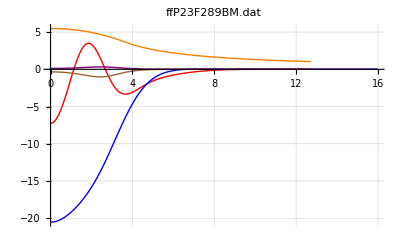

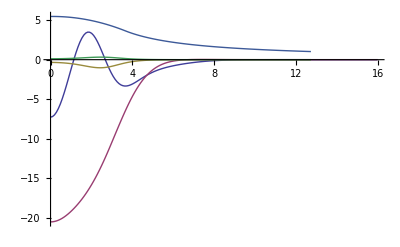

{168,134,134}

```mathematica
test=PotSet[MA,ZA,T,RcA,134,h1,16];
ListPlot[{
RePot[test[[1]]],
ImPot[test[[1]]],
RePot[test[[2]]],
ImPot[test[[2]]],
test[[3]]
}
,Joined->True,PlotRange->All]
{Length[test[[1]]],Length[test[[2]]],Length[test[[2]]]}
```

## GetOgata

```mathematica
GetOgata[filename_,LSfilename_,SkipRow_,Linux_]:=Module[
{RawData,n,DOgata,DLS,DCoul,dir,chdir},
dir=Directory[];
If[dir=="/home/goluckyryan/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata",chdir=0,Print["change dir."];chdir=1];
If[chdir==1,
If[Linux==1 ,
SetDirectory[Directory[]<>"/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata/"],
SetDirectory["D:/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata/"]
];
Print[Directory[]];
];
RawData=Drop[Import[filename],SkipRow];
n=Length[RawData];
DOgata=Table[{RawData [[i,1]],RawData[[i,2]]+ⅈ RawData[[i,3]]},{i,1,n}];
RawData=Drop[Import[LSfilename],SkipRow];
n=Length[RawData];
DLS=Table[{RawData [[i,1]],RawData[[i,2]]+ⅈ RawData[[i,3]]},{i,1,n}];
DCoul=Table[{RawData [[i,1]],RawData[[i,4]]},{i,1,n}];
Print[ListPlot[{
RePot[DOgata],
ImPot[DOgata],
RePot[DLS],
ImPot[DLS],
DCoul},Joined->True,PlotRange->All,PlotLabel->filename,PlotStyle->{Red,Blue,Brown,Purple,Orange},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]];
{DOgata,DLS,DCoul}
]
```